```mathematica
<<PrSAT`
```

Using PrSAT to find a model in which (1) all the independencies in DAG1 and DAG2 hold, (2) Pr[A∧B | a∧b] > Pr[A∧B], and (3) Pr[A∧B|a∧b] < Min[Pr[A|a],Pr[B|b]].

```mathematica
model=PrSAT[{

Pr[A|B]==Pr[A],
Pr[b|a]==Pr[b],
Pr[A|b∧a]==Pr[A|a],
Pr[B|a∧A∧b]==Pr[B|b],
Pr[a|b∧A∧B]==Pr[a|A∧B],
Pr[a|b∧A]==Pr[a|A],
Pr[a|b∧¬A]==Pr[a|¬A],
Pr[a|b∧B]==Pr[a|B],
Pr[a|b∧¬B]==Pr[a|¬B],
Pr[a|B∧A]==Pr[a|A],
Pr[a|B∧¬A]==Pr[a|¬A],
Pr[b|A∧a∧B]==Pr[b|B],
Pr[b|A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧B]==Pr[b|B],
Pr[b|a∧B]==Pr[b|B],

Pr[A∧B|a∧b]>Pr[A∧B],

Pr[A∧B|a∧b]<Pr[A|a],
Pr[A∧B|a∧b]<Pr[B|b],

Pr[A]==1/2,Pr[B]==1/2

},Probabilities->Regular,BypassSearch->True]
```

{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→17/168,𝕒_2→85/1512,𝕒_3→17/216,𝕒_4→5/84,𝕒_5→5/56,𝕒_6→17/216,𝕒_7→25/756,𝕒_8→25/504,𝕒_9→5/108,𝕒_10→5/72,𝕒_11→1/14,𝕒_12→5/108,𝕒_13→5/72,𝕒_14→5/126,𝕒_15→1/18,𝕒_16→1/18}}

```mathematica
AlgebraicForm[{

Pr[A|B]==Pr[A],
Pr[b|a]==Pr[b],
Pr[A|b∧a]==Pr[A|a],
Pr[B|a∧A∧b]==Pr[B|b],
Pr[a|b∧A∧B]==Pr[a|A∧B],
Pr[a|b∧A]==Pr[a|A],
Pr[a|b∧¬A]==Pr[a|¬A],
Pr[a|b∧B]==Pr[a|B],
Pr[a|b∧¬B]==Pr[a|¬B],
Pr[a|B∧A]==Pr[a|A],
Pr[a|B∧¬A]==Pr[a|¬A],
Pr[b|A∧a∧B]==Pr[b|B],
Pr[b|A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧B]==Pr[b|B],
Pr[b|a∧B]==Pr[b|B],

Pr[A∧B|a∧b]>Pr[A∧B],

Pr[A∧B|a∧b]<Pr[A|a],
Pr[A∧B|a∧b]<Pr[B|b],

Pr[A]==1/2,Pr[B]==1/2

},{A,B,a,b}]
```

{(𝕒_10+𝕒_13+𝕒_15+𝕒_16)/(𝕒_5+𝕒_8+𝕒_10+𝕒_11+𝕒_13+𝕒_14+𝕒_15+𝕒_16)==𝕒_3+𝕒_6+𝕒_9+𝕒_10+𝕒_12+𝕒_13+𝕒_15+𝕒_16,(𝕒_7+𝕒_12+𝕒_14+𝕒_16)/(𝕒_2+𝕒_6+𝕒_7+𝕒_8+𝕒_12+𝕒_13+𝕒_14+𝕒_16)==𝕒_4+𝕒_7+𝕒_9+𝕒_11+𝕒_12+𝕒_14+𝕒_15+𝕒_16,(𝕒_12+𝕒_16)/(𝕒_7+𝕒_12+𝕒_14+𝕒_16)==(𝕒_6+𝕒_12+𝕒_13+𝕒_16)/(𝕒_2+𝕒_6+𝕒_7+𝕒_8+𝕒_12+𝕒_13+𝕒_14+𝕒_16),𝕒_16/(𝕒_12+𝕒_16)==(𝕒_11+𝕒_14+𝕒_15+𝕒_16)/(𝕒_4+𝕒_7+𝕒_9+𝕒_11+𝕒_12+𝕒_14+𝕒_15+𝕒_16),𝕒_16/(𝕒_15+𝕒_16)==(𝕒_13+𝕒_16)/(𝕒_10+𝕒_13+𝕒_15+𝕒_16),(𝕒_12+𝕒_16)/(𝕒_9+𝕒_12+𝕒_15+𝕒_16)==(𝕒_6+𝕒_12+𝕒_13+𝕒_16)/(𝕒_3+𝕒_6+𝕒_9+𝕒_10+𝕒_12+𝕒_13+𝕒_15+𝕒_16),(𝕒_7+𝕒_14)/(𝕒_4+𝕒_7+𝕒_11+𝕒_14)==(𝕒_2+𝕒_7+𝕒_8+𝕒_14)/(1-𝕒_3-𝕒_6-𝕒_9-𝕒_10-𝕒_12-𝕒_13-𝕒_15-𝕒_16),(𝕒_14+𝕒_16)/(𝕒_11+𝕒_14+𝕒_15+𝕒_16)==(𝕒_8+𝕒_13+𝕒_14+𝕒_16)/(𝕒_5+𝕒_8+𝕒_10+𝕒_11+𝕒_13+𝕒_14+𝕒_15+𝕒_16),(𝕒_7+𝕒_12)/(𝕒_4+𝕒_7+𝕒_9+𝕒_12)==(𝕒_2+𝕒_6+𝕒_7+𝕒_12)/(1-𝕒_5-𝕒_8-𝕒_10-𝕒_11-𝕒_13-𝕒_14-𝕒_15-𝕒_16),(𝕒_13+𝕒_16)/(𝕒_10+𝕒_13+𝕒_15+𝕒_16)==(𝕒_6+𝕒_12+𝕒_13+𝕒_16)/(𝕒_3+𝕒_6+𝕒_9+𝕒_10+𝕒_12+𝕒_13+𝕒_15+𝕒_16),(𝕒_8+𝕒_14)/(𝕒_5+𝕒_8+𝕒_11+𝕒_14)==(𝕒_2+𝕒_7+𝕒_8+𝕒_14)/(1-𝕒_3-𝕒_6-𝕒_9-𝕒_10-𝕒_12-𝕒_13-𝕒_15-𝕒_16),𝕒_16/(𝕒_13+𝕒_16)==(𝕒_11+𝕒_14+𝕒_15+𝕒_16)/(𝕒_5+𝕒_8+𝕒_10+𝕒_11+𝕒_13+𝕒_14+𝕒_15+𝕒_16),𝕒_12/(𝕒_6+𝕒_12)==(𝕒_4+𝕒_7+𝕒_9+𝕒_12)/(1-𝕒_5-𝕒_8-𝕒_10-𝕒_11-𝕒_13-𝕒_14-𝕒_15-𝕒_16),𝕒_7/(𝕒_2+𝕒_7)==(𝕒_4+𝕒_7+𝕒_9+𝕒_12)/(1-𝕒_5-𝕒_8-𝕒_10-𝕒_11-𝕒_13-𝕒_14-𝕒_15-𝕒_16),𝕒_14/(𝕒_8+𝕒_14)==(𝕒_11+𝕒_14+𝕒_15+𝕒_16)/(𝕒_5+𝕒_8+𝕒_10+𝕒_11+𝕒_13+𝕒_14+𝕒_15+𝕒_16),(𝕒_14+𝕒_16)/(𝕒_8+𝕒_13+𝕒_14+𝕒_16)==(𝕒_11+𝕒_14+𝕒_15+𝕒_16)/(𝕒_5+𝕒_8+𝕒_10+𝕒_11+𝕒_13+𝕒_14+𝕒_15+𝕒_16),𝕒_16/(𝕒_7+𝕒_12+𝕒_14+𝕒_16)>𝕒_10+𝕒_13+𝕒_15+𝕒_16,𝕒_16/(𝕒_7+𝕒_12+𝕒_14+𝕒_16)<(𝕒_6+𝕒_12+𝕒_13+𝕒_16)/(𝕒_2+𝕒_6+𝕒_7+𝕒_8+𝕒_12+𝕒_13+𝕒_14+𝕒_16),𝕒_16/(𝕒_7+𝕒_12+𝕒_14+𝕒_16)<(𝕒_11+𝕒_14+𝕒_15+𝕒_16)/(𝕒_4+𝕒_7+𝕒_9+𝕒_11+𝕒_12+𝕒_14+𝕒_15+𝕒_16),𝕒_3+𝕒_6+𝕒_9+𝕒_10+𝕒_12+𝕒_13+𝕒_15+𝕒_16==1/2,𝕒_5+𝕒_8+𝕒_10+𝕒_11+𝕒_13+𝕒_14+𝕒_15+𝕒_16==1/2}

```mathematica
TruthTable[model]
```

a | A | b | B | var | Pr
T | T | T | T | 𝕒_16 | 1/18
T | T | T | F | 𝕒_12 | 5/108
T | T | F | T | 𝕒_13 | 5/72
T | T | F | F | 𝕒_6 | 17/216
T | F | T | T | 𝕒_14 | 5/126
T | F | T | F | 𝕒_7 | 25/756
T | F | F | T | 𝕒_8 | 25/504
T | F | F | F | 𝕒_2 | 85/1512
F | T | T | T | 𝕒_15 | 1/18
F | T | T | F | 𝕒_9 | 5/108
F | T | F | T | 𝕒_10 | 5/72
F | T | F | F | 𝕒_3 | 17/216
F | F | T | T | 𝕒_11 | 1/14
F | F | T | F | 𝕒_4 | 5/84
F | F | F | T | 𝕒_5 | 5/56
F | F | F | F | 𝕒_1 | 17/168

```mathematica
EvaluateProbability[{

Pr[A|B]==Pr[A],
Pr[b|a]==Pr[b],
Pr[A|b∧a]==Pr[A|a],
Pr[B|a∧A∧b]==Pr[B|b],
Pr[a|b∧A∧B]==Pr[a|A∧B],
Pr[a|b∧A]==Pr[a|A],
Pr[a|b∧¬A]==Pr[a|¬A],
Pr[a|b∧B]==Pr[a|B],
Pr[a|b∧¬B]==Pr[a|¬B],
Pr[a|B∧A]==Pr[a|A],
Pr[a|B∧¬A]==Pr[a|¬A],
Pr[b|A∧a∧B]==Pr[b|B],
Pr[b|A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧B]==Pr[b|B],
Pr[b|a∧B]==Pr[b|B],

Pr[A∧B|a∧b]>Pr[A∧B],

Pr[A∧B|a∧b]-Min[Pr[A|a],Pr[B|b]]

}, model]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,-5/22}

The following function samples n probability distributions at random (assuming  a uniform distribution over all possible distributions).

```mathematica
Distributions[n_]:=Module[{M},
M:={{a->{Subscript[𝕒, 2],Subscript[𝕒, 6],Subscript[𝕒, 7],Subscript[𝕒, 8],Subscript[𝕒, 12],Subscript[𝕒, 13],Subscript[𝕒, 14],Subscript[𝕒, 16]},A->{Subscript[𝕒, 3],Subscript[𝕒, 6],Subscript[𝕒, 9],Subscript[𝕒, 10],Subscript[𝕒, 12],Subscript[𝕒, 13],Subscript[𝕒, 15],Subscript[𝕒, 16]},b->{Subscript[𝕒, 4],Subscript[𝕒, 7],Subscript[𝕒, 9],Subscript[𝕒, 11],Subscript[𝕒, 12],Subscript[𝕒, 14],Subscript[𝕒, 15],Subscript[𝕒, 16]},B->{Subscript[𝕒, 5],Subscript[𝕒, 8],Subscript[𝕒, 10],Subscript[𝕒, 11],Subscript[𝕒, 13],Subscript[𝕒, 14],Subscript[𝕒, 15],Subscript[𝕒, 16]},Ω->{Subscript[𝕒, 1],Subscript[𝕒, 2],Subscript[𝕒, 3],Subscript[𝕒, 4],Subscript[𝕒, 5],Subscript[𝕒, 6],Subscript[𝕒, 7],Subscript[𝕒, 8],Subscript[𝕒, 9],Subscript[𝕒, 10],Subscript[𝕒, 11],Subscript[𝕒, 12],Subscript[𝕒, 13],Subscript[𝕒, 14],Subscript[𝕒, 15],Subscript[𝕒, 16]}},MapThread[Rule,{{Subscript[𝕒, 1],Subscript[𝕒, 2],Subscript[𝕒, 3],Subscript[𝕒, 4],Subscript[𝕒, 5],Subscript[𝕒, 6],Subscript[𝕒, 7],Subscript[𝕒, 8],Subscript[𝕒, 9],Subscript[𝕒, 10],Subscript[𝕒, 11],Subscript[𝕒, 12],Subscript[𝕒, 13],Subscript[𝕒, 14],Subscript[𝕒, 15],Subscript[𝕒, 16]},RandomModel[16]}]};
ParallelTable[M,{n}]
];
```

Here, we generate (a) 1 million random distributions, then (b) we select those which satisfy Pr[A∧B|a∧b] > Pr[A∧B], and (c) we look at a histogram of the values Pr[A∧B|a∧b] – Min[Pr[A|a],Pr[B|b]] on those selected distributions.

```mathematica
DISTs=Distributions[1000000];
ConDISTs=Select[DISTs,EvaluateProbability[Pr[A∧B|a∧b]>Pr[A∧B],#]&];
ConDIFFs=EvaluateProbability[Pr[A∧B|a∧b]-Min[Pr[A|a],Pr[B|b]],#]&/@ConDISTs;
```

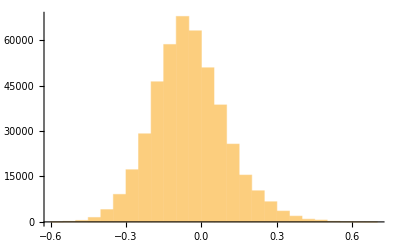

```mathematica
Histogram[ConDIFFs]
```

Finally, we (d) compute the % of distributions on which both Pr[A∧B|a∧b] > Pr[A∧B] and Pr[A∧B|a∧b] < Min[Pr[A|a],Pr[B|b]].

```mathematica
Failures=Select[ConDIFFs,#<0&];
```

```mathematica
Length[Failures]/Length[ConDISTs]//N
```

0.657489

Around 66% of all distributions on which Pr[A∧B|a∧b] > Pr[A∧B] are such that Pr[A∧B | a∧b] < Min[Pr[A|a],Pr[B|b]].  

What about when we add in the independence relations from the DAGs?

Independence constraints are measure zero.  So, we need a different approach for these calculations.  

Let’s just use PrSAT to find a bunch of (randomly sampled) distributions on which (1) all the independencies in DAG1 and DAG2 hold, and (2) Pr[A∧B|a∧b] > Pr[A∧B]; and, then do a histogram of the Pr[A∧B|a∧b] – Min[Pr[A|a],Pr[B|b]] values among those sampled models.

```mathematica
RandomRational[p_]:=Module[{r},
r=RandomReal[{0,1},WorkingPrecision->p];
Rationalize[r,0]
];
```

```mathematica
RandomRational[12]
```

244422/492251

Here, we generate 10,000 randomly sampled distributions on which (1) all the independencies in DAG1 and DAG2 hold, and (2) Pr[A∧B|a∧b] > Pr[A∧B].

```mathematica
INDDISTs=ParallelTable[PrSAT[{

Pr[A|B]==Pr[A],
Pr[b|a]==Pr[b],
Pr[A|b∧a]==Pr[A|a],
Pr[B|a∧A∧b]==Pr[B|b],
Pr[a|b∧A∧B]==Pr[a|A∧B],
Pr[a|b∧A]==Pr[a|A],
Pr[a|b∧¬A]==Pr[a|¬A],
Pr[a|b∧B]==Pr[a|B],
Pr[a|b∧¬B]==Pr[a|¬B],
Pr[a|B∧A]==Pr[a|A],
Pr[a|B∧¬A]==Pr[a|¬A],
Pr[b|A∧a∧B]==Pr[b|B],
Pr[b|A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧B]==Pr[b|B],
Pr[b|a∧B]==Pr[b|B],

Pr[A∧B|a∧b]>Pr[A∧B],

Pr[A]==RandomRational[12],Pr[B]==RandomRational[12],Pr[a]==RandomRational[12],Pr[b]==RandomRational[12]

},Probabilities->Regular,BypassSearch->True],{10000}];
```

Then, we look at a histogram of the Pr[A∧B|a∧b] – Min[Pr[A|a],Pr[B|b]] values on these 10,000 models.

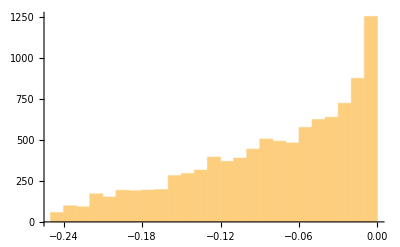

```mathematica
INDDIFFs=EvaluateProbability[Pr[A∧B|a∧b]-Min[Pr[A|a],Pr[B|b]],#]&/@INDDISTs;
Histogram[INDDIFFs]
```

This histogram (which has zero positive values in it) suggests an impossibility result.  

And, it turns out that (3) & (4) together imply that Pr[A∧B|a∧b] must be less than both Pr[A|a]  and Pr[B|b]!

Impossibility Result — Regularity + the two independence assumptions (3) & (4) are jointly incompatible with Pr[A∧B|a∧b] ≥ Min[Pr[A|a],Pr[B|b]].  See my hand proof for an explanation.

```mathematica
PrSAT[{

Pr[A|b∧a]==Pr[A|a],

Pr[B|a∧A∧b]==Pr[B|b],

Pr[A∧B|a∧b]≥Pr[A|a]||Pr[A∧B|a∧b]>=Pr[B|b]

},Probabilities->Regular,BypassSearch->True]
```

{}

Finding all pairs that yield impossibility.

```mathematica
ImpQ[conds_]:=TimeConstrained[PrSAT[conds ∪{

Pr[A∧B|a∧b]≥Pr[A|a]||Pr[A∧B|a∧b]>=Pr[B|b],

Pr[A]==RandomRational[12],Pr[B]==RandomRational[12],Pr[a]==RandomRational[12],Pr[b]==RandomRational[12]

},Probabilities->Regular,BypassSearch->True],10];
```

Check to see the function works by verifying the known pair above.

```mathematica
ImpQ[{Pr[A|b∧a]==Pr[A|a],

Pr[B|a∧A∧b]==Pr[B|b]
}]
```

{}

Now, generate all the 2-element subsets of independence conditions.

```mathematica
PAIRS=Subsets[{Pr[A|B]==Pr[A],
Pr[b|a]==Pr[b],
Pr[A|b∧a]==Pr[A|a],
Pr[B|a∧A∧b]==Pr[B|b],
Pr[a|b∧A∧B]==Pr[a|A∧B],
Pr[a|b∧A]==Pr[a|A],
Pr[a|b∧¬A]==Pr[a|¬A],
Pr[a|b∧B]==Pr[a|B],
Pr[a|b∧¬B]==Pr[a|¬B],
Pr[a|B∧A]==Pr[a|A],
Pr[a|B∧¬A]==Pr[a|¬A],
Pr[b|A∧a∧B]==Pr[b|B],
Pr[b|A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧¬B]==Pr[b|¬B],
Pr[b|¬A∧a∧B]==Pr[b|B],
Pr[b|a∧B]==Pr[b|B]},{2}];
```

```mathematica
Length[PAIRS]
```

120

```mathematica
tests=ParallelTable[ImpQ[PAIRS[[i]]],{i,1,Length[PAIRS]}];
```

```mathematica
tests
```

{{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→58588198281/3705852443584,𝕒_2→58588198281/926463110896,𝕒_3→9100981089660072585882109251211/81035136105270366826236904605824,𝕒_4→58588198281/1852926221792,𝕒_5→2563024782677493777609/80590106816943000921728,𝕒_6→11594531757920019430893244065/254028639828433751806385280896,𝕒_7→58588198281/3705852443584,𝕒_8→142779502391543994060805753575/7366830555024578802385173145984,𝕒_9→6945057903447579780630069449659/40517568052635183413118452302912,𝕒_10→1099556672526491077580587057765/40517568052635183413118452302912,𝕒_11→119512191111/1852926221792,𝕒_12→622819487713523031297848241/15876789989277109487899080056,𝕒_13→14700311060163927/201400748765314336,𝕒_14→1691137633983978215618428515/127014319914216875903192640448,𝕒_15→1099556672526491077580587057765/40517568052635183413118452302912,𝕒_16→2518876848757443275818185955757/10129392013158795853279613075728}},$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→759350400312040343010440581/13801782514465115348697501696,𝕒_2→80971987/247894016,𝕒_3→31506781158233/599007421899776,𝕒_4→724492160489521/512163441109168128,𝕒_5→264663101086525/18868733789842944,𝕒_6→3/8,𝕒_7→5/4096,𝕒_8→25/512,𝕒_9→5/1024,𝕒_10→4842969959017/449255566424832,𝕒_11→22981073/10594055808,𝕒_12→5/512,𝕒_13→3/256,𝕒_14→1/64,𝕒_15→3/128,𝕒_16→3/64}},$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→1815953354242366843/455118862334863267840,𝕒_2→1383611/9162489856,𝕒_3→753570247909/1627650902251520,𝕒_4→753570247909/1627650902251520,𝕒_5→128956785181765726217345776425577/1002352724337233422843861550825472,𝕒_6→753570247909/813825451125760,𝕒_7→5/32768,𝕒_8→3/256,𝕒_9→753570247909/1627650902251520,𝕒_10→128956785181765726217345776425577/1002352724337233422843861550825472,𝕒_11→1939581780073062279082328345348851/5011763621686167114219307754127360,𝕒_12→1/512,𝕒_13→1471734074591989276349557/100211029381495370924252160,𝕒_14→3/128,𝕒_15→243164939593655076655270453545943/1002352724337233422843861550825472,𝕒_16→7/128}},{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→2642105296102891750442551/210043123631236631142629376,𝕒_2→8762057027/38008553472,𝕒_3→70100060148631/595525819908096,𝕒_4→1635645890550395/11020061673215852544,𝕒_5→698751418109501/4817821607039232,𝕒_6→7/64,𝕒_7→5/32768,𝕒_8→1/8,𝕒_9→5/16384,𝕒_10→28687131393191/882654340220928,𝕒_11→282216551/261665109504,𝕒_12→1/2048,𝕒_13→353/2048,𝕒_14→1/512,𝕒_15→1/32,𝕒_16→5/256}},$Aborted,$Aborted,$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→7419484167175325567/189229377575831932768,𝕒_2→32673698356620890781279/10558053121843542688790560,𝕒_3→3719530252555978015/94614688787915966384,𝕒_4→119162439708430127711650326781426291/288049052478321138870111877377171360,𝕒_5→63279/611669344,𝕒_6→31832352600587932176111/10558053121843542688790560,𝕒_7→95497057801763796528333/3018634338434064949498328,𝕒_8→63279/305834672,𝕒_9→5257349985657610420237432119986474881/12674158309046130110284922604595539840,𝕒_10→63279/152917336,𝕒_11→96994873827/129017273887216,𝕒_12→2348040896731199716274907/48298149414945039191973248,𝕒_13→63279/38229334,𝕒_14→96994873827/32254318471804,𝕒_15→96994873827/1032138191097728,𝕒_16→401097674961/1032138191097728}},{},$Aborted,$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→9715635342926103477503381/3964683844365406260049674240,𝕒_2→1225941769520129/19184521896591360,𝕒_3→106382427/402536960,𝕒_4→493096625541235375/19698483559698002688,𝕒_5→6728291385/78467549691904,𝕒_6→3/256,𝕒_7→128039712607/7493953865856,𝕒_8→515/65536,𝕒_9→73/256,𝕒_10→3/128,𝕒_11→25181977/153256932992,𝕒_12→1/64,𝕒_13→5/512,𝕒_14→5/128,𝕒_15→5/32,𝕒_16→5/64}},$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→5352781200043145543943029361/46383654137087469129140756480,𝕒_2→101856972367/198526168637440,𝕒_3→59552513/301446569984,𝕒_4→92419135316013/2878629445242880,𝕒_5→25062339418502741/151592077557207168,𝕒_6→5/8192,𝕒_7→595328309711/12407885539840,𝕒_8→1/2,𝕒_9→3/4096,𝕒_10→1099512671/791297246208,𝕒_11→1/32,𝕒_12→1/512,𝕒_13→5/1024,𝕒_14→7/128,𝕒_15→3/256,𝕒_16→1/32}},$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→65201606886488305041564073/552799436149443177971426304,𝕒_2→603793562951/123315143922432,𝕒_3→12368467/600649216,𝕒_4→758768911/2934684672,𝕒_5→253497394663001/1280986924643328,𝕒_6→1/1024,𝕒_7→5/1024,𝕒_8→3/512,𝕒_9→3/128,𝕒_10→5/128,𝕒_11→97254538383923150297/471212321216972848128,𝕒_12→1/512,𝕒_13→5/1024,𝕒_14→2589953317169/493260575689728,𝕒_15→3/32,𝕒_16→7/512}},{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→79658810287231/3116831711289600,𝕒_2→5/128,𝕒_3→2807003314696555393/476066000824571731200,𝕒_4→303380777/3888626944,𝕒_5→89276999560701/2208232638375808,𝕒_6→1833860211321/296975141651584,𝕒_7→7/64,𝕒_8→3/64,𝕒_9→3/256,𝕒_10→3/128,𝕒_11→319048643987823254565/2255518627977668364608,𝕒_12→1/64,𝕒_13→1/32,𝕒_14→7201882970781/74243785412896,𝕒_15→7/64,𝕒_16→7/32}},$Aborted,$Aborted,{},$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→6965647889158258051/111896693180085141504,𝕒_2→181/1024,𝕒_3→7399122798548655064545/21035892540357823340929024,𝕒_4→3842975667977/28749799768064,𝕒_5→1533241/15941984256,𝕒_6→26462730285/6442517430272,𝕒_7→97/256,𝕒_8→3/32768,𝕒_9→1490380159388103508971091/6573716418861819794040320,𝕒_10→7/32768,𝕒_11→7/16384,𝕒_12→9689959817/2013286696960,𝕒_13→7/8192,𝕒_14→3/2048,𝕒_15→7/2048,𝕒_16→3/512}},{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→945916122337300477292822622303820073/2902427911958149576184962766161313792,𝕒_2→62898591330651/2023073129168896,𝕒_3→2416155349/132535353344,𝕒_4→33090926057636407910362110277/179398846080320609071580512256,𝕒_5→243235887601/18282975171444736,𝕒_6→13/128,𝕒_7→14491010101807/252884141146112,𝕒_8→7/524288,𝕒_9→1/32,𝕒_10→3/131072,𝕒_11→56625830793/2285371896430592,𝕒_12→1/8,𝕒_13→3/131072,𝕒_14→7/65536,𝕒_15→1/16,𝕒_16→1/16}},$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→12553160436310099130078788849/50266866261553498838174287872,𝕒_2→1079017747/6553290752,𝕒_3→276719/54040192,𝕒_4→59966975/38186858496,𝕒_5→292168207700983/4069710147271776,𝕒_6→3/512,𝕒_7→3/2048,𝕒_8→1/16,𝕒_9→3/1024,𝕒_10→3/32,𝕒_11→319980845/33413501184,𝕒_12→7/1024,𝕒_13→3/16,𝕒_14→5/256,𝕒_15→5/128,𝕒_16→5/64}},$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→32417705169994073/742065622145679360,𝕒_2→5/16384,𝕒_3→18313665561434567452409/1365572308366357075353600,𝕒_4→16729949/23049093120,𝕒_5→101840643075/263741464576,𝕒_6→3425789/13210214400,𝕒_7→3/16384,𝕒_8→7/8192,𝕒_9→1/1024,𝕒_10→11144810012282938171347/24819180907236006663680,𝕒_11→3/64,𝕒_12→1/4096,𝕒_13→1/512,𝕒_14→1/256,𝕒_15→298041/7502960,𝕒_16→3/256}},{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→1225761903452611729659855629/1926052102411345759691819016192,𝕒_2→6434457648314603073/112666428620135931904,𝕒_3→2298580022488356295/17835570567203252224,𝕒_4→7255385/4471627776,𝕒_5→23550884836908493/7065001045584480768,𝕒_6→49/2048,𝕒_7→3/8192,𝕒_8→31/512,𝕒_9→1/512,𝕒_10→17/64,𝕒_11→585677/69869184,𝕒_12→1/256,𝕒_13→264141306811/808940438816,𝕒_14→1/64,𝕒_15→5/128,𝕒_16→1/16}},$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,{{a→{𝕒_2,𝕒_6,𝕒_7,𝕒_8,𝕒_12,𝕒_13,𝕒_14,𝕒_16},A→{𝕒_3,𝕒_6,𝕒_9,𝕒_10,𝕒_12,𝕒_13,𝕒_15,𝕒_16},b→{𝕒_4,𝕒_7,𝕒_9,𝕒_11,𝕒_12,𝕒_14,𝕒_15,𝕒_16},B→{𝕒_5,𝕒_8,𝕒_10,𝕒_11,𝕒_13,𝕒_14,𝕒_15,𝕒_16},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8,𝕒_9,𝕒_10,𝕒_11,𝕒_12,𝕒_13,𝕒_14,𝕒_15,𝕒_16}},{𝕒_1→29199990912983924405730129285949/581219732326554305639597642219520,𝕒_2→160362465/285381361664,𝕒_3→10487993750131/1055930306396160,𝕒_4→50949591194759459544253463/66736692536004016195338240,𝕒_5→5884055199/4463872491520,𝕒_6→5/131072,𝕒_7→3/32768,𝕒_8→27/16384,𝕒_9→1317587934599/16498911037440,𝕒_10→3/1024,𝕒_11→108877601/69748007680,𝕒_12→1/2048,𝕒_13→3/512,𝕒_14→3/256,𝕒_15→3/128,𝕒_16→3/64}},$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted,$Aborted}

```mathematica
Position[tests,{}]
```

{{17},{30}}

```mathematica
Position[tests,$Aborted]
```

{{2},{3},{4},{5},{6},{8},{9},{12},{13},{14},{15},{18},{19},{20},{22},{24},{25},{28},{29},{31},{32},{35},{36},{37},{38},{39},{40},{41},{42},{44},{45},{46},{47},{48},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120}}

```mathematica
PAIRS[[17]]
```

{Pr[b|a]==Pr[b],Pr[B|a&&A&&b]==Pr[B|b]}

```mathematica
PAIRS[[30]]
```

{Pr[A|b&&a]==Pr[A|a],Pr[B|a&&A&&b]==Pr[B|b]}

Another conjunction principle

	If 𝔼 confirms 𝕏 and 𝔼 confirms 𝕐, then 𝔼 confirms 𝕏∧𝕐.  

This is not generally true, of course.

```mathematica
PrSAT[{

Pr[𝕏|𝔼]>Pr[𝕏],
Pr[𝕐|𝔼]>Pr[𝕐],

Pr[𝕏∧𝕐|𝔼]≤Pr[𝕏∧𝕐],

Pr[𝕏]==1/2,Pr[𝔼]==1/2

},Probabilities->Regular,BypassSearch->True]
```

{{𝔼→{𝕒_2,𝕒_5,𝕒_6,𝕒_8},𝕏→{𝕒_3,𝕒_5,𝕒_7,𝕒_8},𝕐→{𝕒_4,𝕒_6,𝕒_7,𝕒_8},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8}},{𝕒_1→1/4,𝕒_2→1/16,𝕒_3→3/32,𝕒_4→1/16,𝕒_5→7/32,𝕒_6→1/8,𝕒_7→3/32,𝕒_8→3/32}}

But, if we add the assumption that 𝔼 screens-off 𝕏 from 𝕐, then we do get a theorem.

```mathematica
PrSAT[{

Pr[𝕏|𝔼]>Pr[𝕏],
Pr[𝕐|𝔼]>Pr[𝕐],

Pr[𝕐|𝕏∧𝔼]==Pr[𝕐|𝔼],
Pr[𝕐|𝕏∧¬𝔼]==Pr[𝕐|¬𝔼],

Pr[𝕏∧𝕐|𝔼]≤Pr[𝕏∧𝕐],

Pr[𝕏]==1/2,Pr[𝔼]==1/2

},Probabilities->Regular]
```

PrSAT::srchfail: Search phase failed; attempting FindInstance

{}

Transitivity of Confirmation

If 𝕏 confirms 𝕐 and 𝕐 confirms ℤ, then 𝕏 confirms ℤ.  

Of course, this fails in general.

```mathematica
PrSAT[{
Pr[𝕐|𝕏]>Pr[𝕐],
Pr[ℤ|𝕐]>Pr[ℤ],
Pr[ℤ|𝕏]≤Pr[ℤ],

Pr[𝕏]==1/2,Pr[𝕐]==1/2
},Probabilities->Regular,BypassSearch->True]
```

{{𝕏→{𝕒_2,𝕒_5,𝕒_6,𝕒_8},𝕐→{𝕒_3,𝕒_5,𝕒_7,𝕒_8},ℤ→{𝕒_4,𝕒_6,𝕒_7,𝕒_8},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8}},{𝕒_1→7/32,𝕒_2→1/16,𝕒_3→1/32,𝕒_4→3/32,𝕒_5→3/16,𝕒_6→1/8,𝕒_7→5/32,𝕒_8→1/8}}

But, if we assume that 𝕐 screens-off 𝕏 from ℤ, then this is a theorem.

```mathematica
PrSAT[{
Pr[𝕐|𝕏]>Pr[𝕐],
Pr[ℤ|𝕐]>Pr[ℤ],
Pr[ℤ|𝕏]≤Pr[ℤ],

Pr[ℤ|𝕏∧𝕐]==Pr[ℤ|𝕐],
Pr[ℤ|𝕏∧¬𝕐]==Pr[ℤ|¬𝕐]
},Probabilities->Regular,BypassSearch->True]
```

{}

Special Consequence Condition

If 𝕏 confirms 𝕐 and 𝕐 ⊨ ℤ, then 𝕏 confirms ℤ.

Of course, this fails in general (even assuming Pr[𝕐] > 0, and 0 < Pr[ℤ|𝕏] ≤ Pr[ℤ] < 1).

```mathematica
PrSAT[{
Pr[𝕐|𝕏]>Pr[𝕐]>0,
Pr[ℤ|𝕐]==1,
0<Pr[ℤ|𝕏]≤Pr[ℤ]<1
},BypassSearch->True]
```

{{𝕏→{𝕒_2,𝕒_5,𝕒_6,𝕒_8},𝕐→{𝕒_3,𝕒_5,𝕒_7,𝕒_8},ℤ→{𝕒_4,𝕒_6,𝕒_7,𝕒_8},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8}},{𝕒_1→5/128,𝕒_2→27/128,𝕒_3→0,𝕒_4→1/4,𝕒_5→0,𝕒_6→0,𝕒_7→0,𝕒_8→1/2}}

But, if we assume that 𝕐 screens-off 𝕏 from ℤ, then this is a theorem (assuming Pr[𝕐] > 0, and 0 < Pr[ℤ|𝕏] ≤ Pr[ℤ] < 1).

```mathematica
PrSAT[{
Pr[𝕐|𝕏]>Pr[𝕐]>0,
Pr[ℤ|𝕐]==1,
0<Pr[ℤ|𝕏]≤Pr[ℤ]<1,

Pr[ℤ|𝕏∧𝕐]==Pr[ℤ|𝕐],
Pr[ℤ|𝕏∧¬𝕐]==Pr[ℤ|¬𝕐]
},BypassSearch->True]
```

{}

Simpson’s Paradox

If 𝕏 confirms 𝕐, given ℤ and 𝕏 confirms 𝕐, given ¬ℤ, then 𝕏 confirms 𝕐 (unconditionally).  

Of course, this fails in general.

```mathematica
PrSAT[{
Pr[𝕐|𝕏∧ℤ]>Pr[𝕐|ℤ],
Pr[𝕐|𝕏∧¬ℤ]>Pr[𝕐|¬ℤ],
Pr[𝕐|𝕏]≤Pr[𝕐],

Pr[𝕏]==1/2,Pr[𝕐]==1/2
},Probabilities->Regular,BypassSearch->True]
```

{{𝕏→{𝕒_2,𝕒_5,𝕒_6,𝕒_8},𝕐→{𝕒_3,𝕒_5,𝕒_7,𝕒_8},ℤ→{𝕒_4,𝕒_6,𝕒_7,𝕒_8},Ω→{𝕒_1,𝕒_2,𝕒_3,𝕒_4,𝕒_5,𝕒_6,𝕒_7,𝕒_8}},{𝕒_1→13/256,𝕒_2→3/256,𝕒_3→15/64,𝕒_4→3/16,𝕒_5→1/8,𝕒_6→1/4,𝕒_7→7/256,𝕒_8→29/256}}

But, if we assume that 𝕏 and ℤ are independent, then this is a theorem.

```mathematica
PrSAT[{
Pr[𝕐|𝕏∧ℤ]>Pr[𝕐|ℤ],
Pr[𝕐|𝕏∧¬ℤ]>Pr[𝕐|¬ℤ],
Pr[𝕐|𝕏]≤Pr[𝕐],

Pr[ℤ|𝕏]==Pr[ℤ],

Pr[𝕏]==1/2
},Probabilities->Regular,BypassSearch->True]
```

{}